# COFLASY-M: COsmological evolution of FLavour ASYmmetries - Mathematica

by Valerie Domcke (valerie.domcke@cern.ch), Miguel Escudero (miguel.escudero@cern.ch), Mario Fernandez Navarro (Mario.FernandezNavarro@glasgow.ac.uk), Stefan Sandner (stefan.sandner@lanl.gov)

If you use this code for scientific publications, please cite the paper:

“Lepton Flavour Asymmetries: from the early Universe to BBN.”  Valerie Domcke, Miguel Escudero, Mario Fernandez Navarro and Stefan Sandner,
[JHEP 06, 137] ( https://link.springer.com/article/10.1007/JHEP06(2025)137 ), [arXiv:2502.14960] ( https://arxiv.org/abs/2502.14960 ), [INSPIRE] ( https://inspirehep.net/literature/2893306 ).

“A Limit on the Total Lepton Number in the Universe from BBN and the CMB.” Valerie Domcke, Miguel Escudero, Mario Fernandez Navarro and Stefan Sandner, [arxiv:2510.02438]. (https://arxiv.org/abs/2510.02438).

Last major update: 09-07-2025
v1.2

### Basic instructions

The code works as follows:

	1) Evaluate the “Basic module” section.
	2) The “Examples” section serves as a tutorial to use the code and generates some of the plots in [2502.14960]. Evaluating the full section may take around 15 min, some examples take only a few seconds while others    	take several minutes.

### Basic module

```mathematica
(* Load the basic module which contains all equations and functions to solve the system, takes around 10 seconds *)

ClearAll["Global`*"](*To clear your kernel before loading the basic module*)
ClearSystemCache[]
SetDirectory[NotebookDirectory[]];
Get["BasicModule.m"]
```

### Examples

#### Benchmarks of the paper with FD collisions

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: 0.000213501

Thermodynamics are output to: output/output.dat

Total execution time: 6.901 s

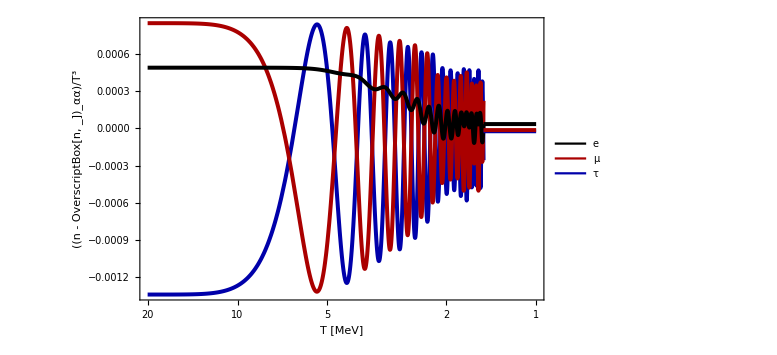

```mathematica
(*We provide initial conditions over (A,ϕ)*)
Aval=0.01;
ϕval=π/3;
(*We translate from (A,ϕ) to (ξe,ξμ,ξτ), alternatively the user may provide conditions over (ξe,ξμ,ξτ) directly*)
ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];

(*This is the minimum input required to run the solving functions, with all the optional arguments using default values*)
(*We run the system with FD collisions*)
Fig5aFD=solveFD[ξeini,ξμini,ξτini]
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: -0.0250915

Thermodynamics are output to: output/Fig5b.dat

Total execution time: 1.204 min

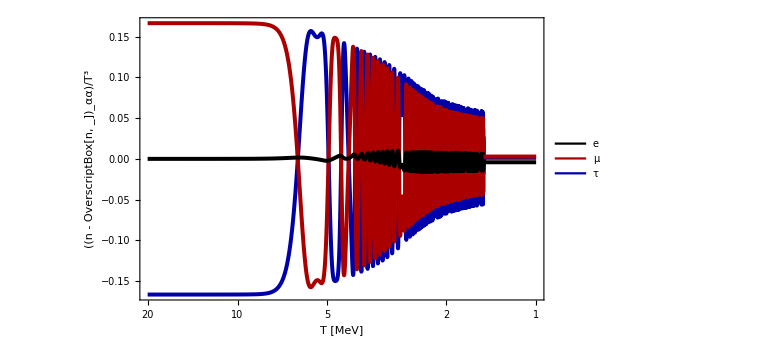

```mathematica
(*Alternatively, the user can define all the optional arguments to be used by the solving functions*)

Aval=√2;
ϕval=π/2;

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];

(*As optional arguments, we provide a name for the .dat file containing the output (filename), initial temperature (Tini), temperature at which oscillation average is taken (Tave), and we extend asymptotically the result at Tave until a final temperature (Tfinal).*)
(*Note we must provide Tini < Tave <= Tfinal for consistency.*)
(*We also provide accuracy (accval) and precision (precval) settings for NDSolve. The solving method (solverMethod) used by NDSolve may also be specified.*)
(*adiabatic->False runs the full system, while adiabatic->True runs the system in the adiabatic approximationw where Vs=0. Finally,timeoutAdiabatic is the execution time in seconds after which the solver switches to the adiabatic approximation, useful for numerically challenging benchmarks.*)

Fig5bFD=solveFD[ξeini,ξμini,ξτini,filename->"Fig5b",Tini->20MeV,Tave->1.5MeV,Tfinal->1MeV,accval->8,precval->8,solverMethod->"BDF",adiabatic->False,timeoutAdiabatic->300]
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: 0.233341

Thermodynamics are output to: output/output.dat

Total execution time: 2.078 min

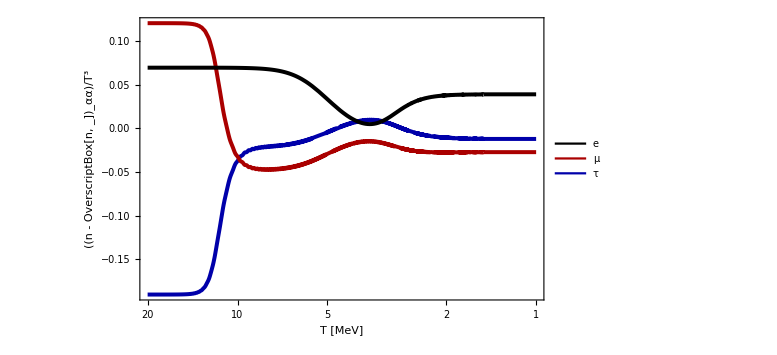

```mathematica
Aval=√2;
ϕval=π/3;

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];

Fig3aFD=solveFD[ξeini,ξμini,ξτini]
```

Starting evolution of the full system

Timeout of 180s reached at T= 1.94841 MeV → Switching to adiabatic V_s=0

System evolved until T_ave=1.5 MeV

Final ξe: 0.00528693

Thermodynamics are output to: output/output.dat

Total execution time: 3.733 min

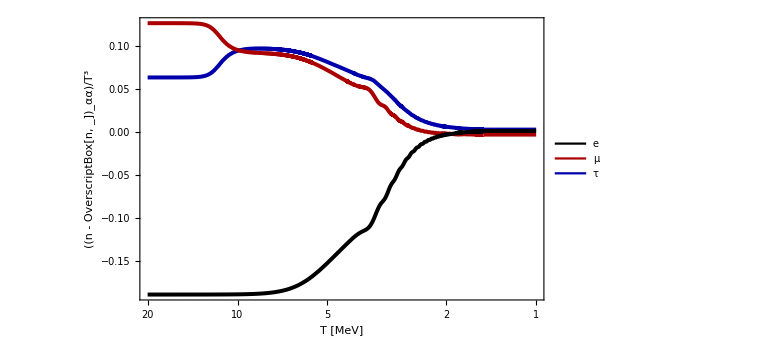

```mathematica
(*This benchmark is more numerically challenging and the solver gets stuck around T=2MeV, but fortunately the timeout switches to adiabatic and allows to reach Tave=1.5MeV*)

Aval=√2;
ϕval=ArcTan[-3,2];

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];

Fig3bFD=solveFD[ξeini,ξμini,ξτini,timeoutAdiabatic->180]
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: 0.215108

Thermodynamics are output to: output/output.dat

Total execution time: 4.646 min

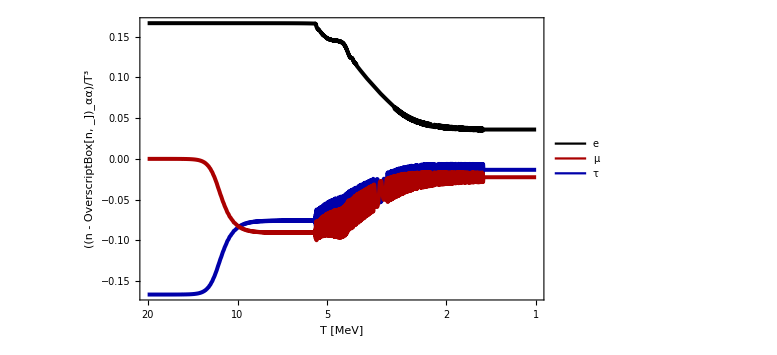

```mathematica
Aval=√2;
ϕval=0;

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];

Fig6aFD=solveFD[ξeini,ξμini,ξτini]
```

#### Benchmarks of the paper with collision terms in the damping approximation

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: 0.0000765606

Thermodynamics are output to: output/output.dat

Total execution time: 1.948 s

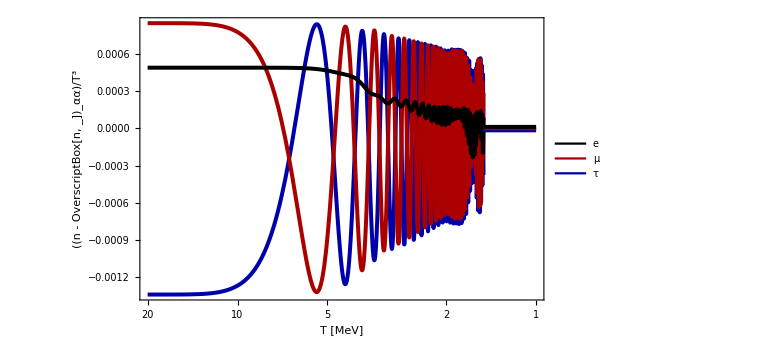

```mathematica
(*Running in the damping approximation is typically much faster*)
Aval=0.01;
ϕval=π/3;

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];

(*The function solveDamping receives the same arguments as solveFD*)
Fig5aD=solveDamping[ξeini,ξμini,ξτini,accval->10,precval->10]
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: -0.0190749

Thermodynamics are output to: output/output.dat

Total execution time: 18.57 s

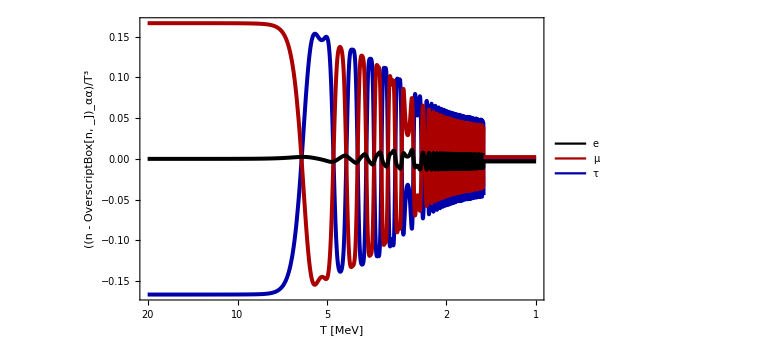

```mathematica
Aval=√2;
ϕval=π/2;

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];

Fig5bD=solveDamping[ξeini,ξμini,ξτini,accval->10,precval->10]
```

```mathematica
(*The next two benchmarks work better with StiffnessSwitching than with BDF*)
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: 0.0120714

Thermodynamics are output to: output/output.dat

Total execution time: 1.229 min

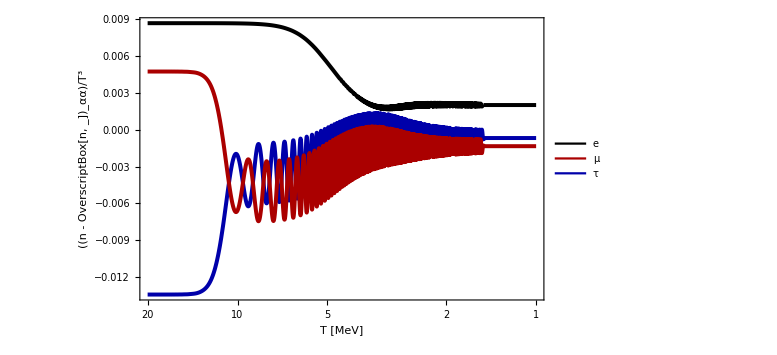

```mathematica
Aval=0.1;
ϕval=0.5;
ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];

Fig12a=solveDamping[ξeini,ξμini,ξτini,solverMethod->"StiffnessSwitching"]
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: 0.122709

Thermodynamics are output to: output/output.dat

Total execution time: 1.704 min

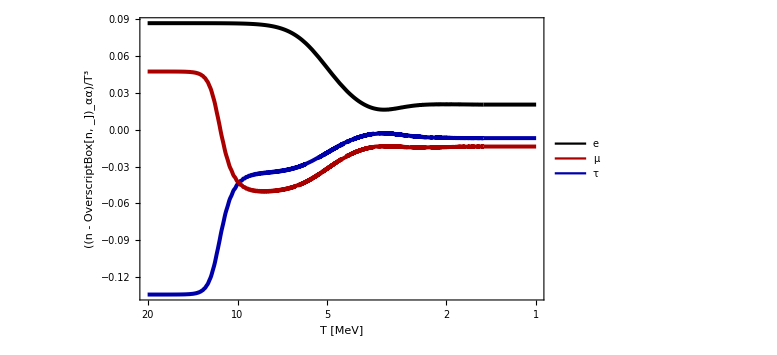

```mathematica
Aval=1;
ϕval=0.5;

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];

Fig12b=solveDamping[ξeini,ξμini,ξτini,solverMethod->"StiffnessSwitching"]
```